## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/faces/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /home/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.120488 GB

seed file: /home/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: dtopa-latitude-5491,  MM v. 12.0.0 for Linux x86

date: Feb 24, 2020, time: 14:50:40

nb: /home/dantopa/Mathematica_files/nb/ert/mercury/faces/scraper-06.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.120488 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## 0 conversion

```mathematica
c=299792458;
```

```mathematica
(* 30 MHz *)
```

```mathematica
c/30000000//N
```

9.99308

```mathematica
(* 3 MHz *)
```

```mathematica
c/3000000//N
```

99.9308

```mathematica
c/50//N
```

5.99585×10^6

```mathematica
c/20//N
```

1.49896×10^7

## 1 read E fields from *.txt file

```mathematica
file="sphereCoarse.4112";
```

```mathematica
file="sphereFine.4112";
```

```mathematica
file="sphereSuperFine.4112";
file="PTW.4112";
file="repaired-mesh.4112"
```

repaired-mesh.4112

### point to file

```mathematica
dirMoM="/Users/dantopa/Dropbox/2nd-generation/RCS-project/linux/ubuntu/";
```

```mathematica
dirMoM=dirData;
```

### read file to scan for data sets

```mathematica
strmList=Import[dirMoM<>file<>".txt","Data"]
title="Sciacca AirFrame";
Λ=Dimensions[strmList]
```

{ ,---| Run Date: February  18, 2020;    Time: 16:03:53,14868,--------------------------------------------------------------------------------}
 |  |  |  |

{14871}

## 2 find table

### tag data sets: record line numbers

```mathematica
(* each data set represents a unique frequency *)
```

```mathematica
census={};
Table[
If[StringContainsQ[strmList[[k]],"Theta, Phi, Theta-Theta"],AppendTo[census,k]]
,{k,Length[strmList]}];
census
m=Length[census]
```

{492,1007,1522,2037,2552,3067,3582,4097,4612,5127,5642,6157,6672,7187,7702,8217,8732,9247,9762,10277,10792,11307,11822,12337,12852,13367,13882,14397}

28

#### empty containers for E field values

```mathematica
θθ={};
θϕ={};
ϕθ={};
ϕϕ={};
```

### harvest frequencies

```mathematica
frequencies={};
Table[
If[StringContainsQ[strmList[[k]],"Freq   ="],AppendTo[frequencies,StringSplit[strmList[[k]]]]]
,{k,Length[strmList]}];
frequencies;
```

```mathematica
list=#[[3]]&/@frequencies
```

{3.00E+00,4.00E+00,5.00E+00,6.00E+00,7.00E+00,8.00E+00,9.00E+00,10.00E+00,11.00E+00,12.00E+00,13.00E+00,14.00E+00,15.00E+00,16.00E+00,17.00E+00,18.00E+00,19.00E+00,20.00E+00,21.00E+00,22.00E+00,23.00E+00,24.00E+00,25.00E+00,26.00E+00,27.00E+00,28.00E+00,29.00E+00,30.00E+00}

```mathematica
ToExpression[list[[22]]]
```

65.2388

```mathematica
Read[StringToStream[#]]&/@list
```

{8.15485,10.8731,13.5914,16.3097,19.028,21.7463,24.4645,27.1828,29.9011,32.6194,35.3377,38.0559,40.7742,43.4925,46.2108,48.9291,51.6474,54.3656,57.0839,59.8022,62.5205,65.2388,67.957,70.6753,73.3936,76.1119,78.8302,81.5485}

```mathematica
Read[StringToStream[list[[2]]]]
```

10.8731

### harvest field values

```mathematica
nAngles=360;
```

```mathematica
Do[
myLine=census[[k]]+1;
fields=Table[
str=StringSplit[strmList[[myLine+j]]];
str=StringReplace[#,","->""]&/@str;
str=StringReplace[#,"("->""]&/@str;
str=StringReplace[#,")"->""]&/@str;
str=StringReplace[#,"{"->""]&/@str;
str=StringReplace[#,"}"->""]&/@str;
tbl=Read[StringToStream[#],Number]&/@Flatten[str]
,{j,nAngles}];
AppendTo[θθ,fields[[All,3]]+ⅈ fields[[All,4]]];
AppendTo[θϕ,fields[[All,5]]+ⅈ fields[[All,6]]];
AppendTo[ϕθ,fields[[All,7]]+ⅈ fields[[All,8]]];
AppendTo[ϕϕ,fields[[All,9]]+ⅈ fields[[All,10]]];
,{k,m}];
```

## 2 extract data

### magnitude

```mathematica
magVV=Map[Abs,θθ,1];
magVH=Map[Abs,θϕ,1];
magHV=Map[Abs,ϕθ,1];
magHH=Map[Abs,ϕϕ,1];
```

### phase

```mathematica
argVV=Map[Arg,θθ,1];
argVH=Map[Arg,θϕ,1];
argHV=Map[Arg,ϕθ,1];
argHH=Map[Arg,ϕϕ,1];
```

### re

```mathematica
reVV=Map[Re,θθ,1];
reVH=Map[Re,θϕ,1];
reHV=Map[Re,ϕθ,1];
reHH=Map[Re,ϕϕ,1];
```

### im

```mathematica
imVV=Map[Im,θθ,1];
imVH=Map[Im,θϕ,1];
imHV=Map[Im,ϕθ,1];
imHH=Map[Im,ϕϕ,1];
```

## 3 table of extrema

### magnitude

```mathematica
fVV=Flatten[magVV];
fVH=Flatten[magVH];
fHV=Flatten[magHV];
fHH=Flatten[magHH];
```

```mathematica
extrema=TableForm[
{{Max[fVV],Max[fVH],Max[fHV],Max[fHH]},{Min[fVV],Min[fVH],Min[fHV],Min[fHH]}},
,TableHeadings->{{"max","min"},{"VV","VH","HV","HH"}}]
```

| VV | VH | HV | HH
max | 52.7233 | 1.05504 | 1.05504 | 83.1007
min | 0.0876739 | 0.000559278 | 0.000557932 | 0.222488

### argument

```mathematica
fVV=Flatten[argVV];
fVH=Flatten[argVH];
fHV=Flatten[argHV];
fHH=Flatten[argHH];
```

```mathematica
extrema=TableForm[
{{Max[fVV],Max[fVH],Max[fHV],Max[fHH]},{Min[fVV],Min[fVH],Min[fHV],Min[fHH]}},
,TableHeadings->{{"max","min"},{"VV","VH","HV","HH"}}]
```

| VV | VH | HV | HH
max | 3.14155 | 3.14085 | 3.1408 | 3.14044
min | -3.13876 | -3.14079 | -3.14061 | -3.14158

### re

```mathematica
fVV=Flatten[reVV];
fVH=Flatten[reVH];
fHV=Flatten[reHV];
fHH=Flatten[reHH];
```

```mathematica
extrema=TableForm[
{{Max[fVV],Max[fVH],Max[fHV],Max[fHH]},{Min[fVV],Min[fVH],Min[fHV],Min[fHH]}},
,TableHeadings->{{"max","min"},{"VV","VH","HV","HH"}}]
```

| VV | VH | HV | HH
max | 52.3215 | 0.94103 | 0.94104 | 80.084
min | -37.5674 | -0.729578 | -0.729575 | -74.5755

### im

```mathematica
fVV=Flatten[imVV];
fVH=Flatten[imVH];
fHV=Flatten[imHV];
fHH=Flatten[imHH];
```

```mathematica
extrema=TableForm[
{{Max[fVV],Max[fVH],Max[fHV],Max[fHH]},{Min[fVV],Min[fVH],Min[fHV],Min[fHH]}},
,TableHeadings->{{"max","min"},{"VV","VH","HV","HH"}}]
```

| VV | VH | HV | HH
max | 52.7232 | 0.852264 | 0.852276 | 70.4328
min | -37.8234 | -0.807951 | -0.807952 | -81.6314

## 4 plot E fields

```mathematica
νticks={{1,3},{8,10},{18,20},{28,30}};
λticks={{1,100},{15,20},{4,50},{28,10}};θticks={{1,0},{91,π/4},{181,π/2},{271,(3π)/4},{361,2π}};
θticks={{1,0},{91,90},{181,180},{271,270},{361,360}};
```

### magnitude

```mathematica
Clear[myPlot];
myPlot[ψ_,str_String,options___]:=Module[{g},
g=MatrixPlot[ψ,
options,
AspectRatio->0.5,
ColorFunction->Hue,
FrameLabel->{{"view",title<>lf<>str},{"ν (MHz)","λ (m)"}},
FrameTicks->{{νticks,λticks},{θticks,None}}];
Return[g];
]
```

```mathematica
g001=myPlot[magVV,"Energy Magnitude (VV)"];
g002=myPlot[magVH,"Energy Magnitude (VH)"];
g003=myPlot[magHV,"Energy Magnitude (HV)"];
g004=myPlot[magHH,"Energy Magnitude (HH)"];
```

### argument

```mathematica
g101=myPlot[argVV,"Complex Argument (VV)"];
g102=myPlot[argVH,"Complex Argument (VH)"];
g103=myPlot[argHV,"Complex Argument (HV)"];
g104=myPlot[argHH,"Complex Argument (HH)"];
```

### real part

```mathematica
g201=myPlot[reVV,"Real Part (VV)"];
g202=myPlot[reVH,"Real Part (VH)"];
g203=myPlot[reHV,"Real Part (HV)"];
g204=myPlot[reHH,"Real Part (HH)"];
```

### imaginary part

```mathematica
g301=myPlot[imVV,"Imaginary Part (VV)"];
g302=myPlot[imVH,"Imaginary Part (VH)"];
g303=myPlot[imHV,"Imaginary Part (HV)"];
g304=myPlot[imHH,"Imaginary Part (HH)"];
```

## 5 export

```mathematica
tresExport[title<>" VV-mag",g001];
tresExport[title<>" VH-mag",g002];
tresExport[title<>" HV-mag",g003];
tresExport[title<>" HH-mag",g004];
```

```mathematica
Clear[g001];
Clear[g002];
Clear[g003];
Clear[g004];
```

### magnitude

```mathematica
tresExport[title<>" VV-mag",g001];
tresExport[title<>" VH-mag",g002];
tresExport[title<>" HV-mag",g003];
tresExport[title<>" HH-mag",g004];
```

```mathematica
Clear[g001,g002,g003,g004];
```

### argument

```mathematica
tresExport[title<>" VV-arg",g101];
tresExport[title<>" VH-arg",g102];
tresExport[title<>" HV-arg",g103];
tresExport[title<>" HH-arg",g104];
```

```mathematica
Clear[g101,g102,g103,g104];
```

### re

```mathematica
tresExport[title<>" VV-re",g201];
tresExport[title<>" VH-re",g202];
tresExport[title<>" HV-re",g203];
tresExport[title<>" HH-re",g204];
```

```mathematica
Clear[g201,g202,g203,g204];
```

### im

```mathematica
tresExport[title<>" VV-im",g301];
tresExport[title<>" VH-im",g302];
tresExport[title<>" HV-im",g303];
tresExport[title<>" HH-im",g304];
```

```mathematica
Clear[g301,g302,g303,g304];
```

## is there a better way to plot?

```mathematica
plots={g001,g002,g003,g004};
```

```mathematica
endings={".png",".pdf",".eps"}
titles={" VV-mag"," VH-mag"," HV-mag"," HH-mag"};
Do[
suffix=endings[[k]];
Print["Preparing ",suffix];
Do[
myTitle=title<>titles[[j]];
plot=plots[[j]];
Print["j = ",j,": ",dirGraph<>myTitle<>suffix];
Export[dirGraph<>myTitle<>suffix,plot];
,{j,Length[plots]}]
,{k,Length[endings]}]
```

{.png,.pdf,.eps}

Preparing .png

j = 1: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack VV-mag.png

j = 2: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack VH-mag.png

j = 3: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack HV-mag.png

j = 4: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack HH-mag.png

Preparing .pdf

j = 1: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack VV-mag.pdf

j = 2: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack VH-mag.pdf

j = 3: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack HV-mag.pdf

j = 4: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack HH-mag.pdf

Preparing .eps

j = 1: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack VV-mag.eps

j = 2: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack VH-mag.eps

j = 3: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack HV-mag.eps

j = 4: /Users/dantopa/Mathematica_files/io/ert/mercury/parse/graphics/Bonito-19 Fast Attack HH-mag.eps

```mathematica
plot
```

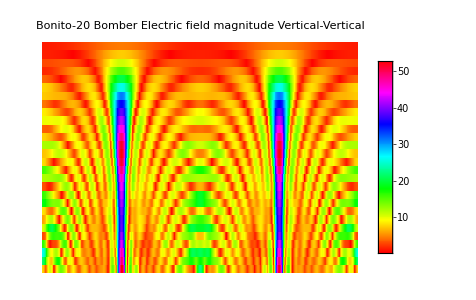

```mathematica
ArrayPlot[magVV,
ColorFunction->Hue,
FrameTicks->{{{1,3},15,20,{28,30}},{0,90,180,270,360},{{1,100},{4,50},{13,20},{28,10}},None},
FrameLabel->{"Frequency MHZ","Angle","Wavelength m",None},
PlotLabel->"Bonito-20 Bomber"<>lf<>"Electric field magnitude Vertical-Vertical",
AspectRatio->3/4,
PlotLegends->Placed[Automatic,After]]
```

```mathematica
Dimensions[magVV]
```

{28,360}

```mathematica
Max[magVV]
```

52.7233

```mathematica
clicks=Range[3,30]
Length[%]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

28

```mathematica
z={Range[28],Range[3,30]}ᵀ//mf
```

(1 | 3
2 | 4
3 | 5
4 | 6
5 | 7
6 | 8
7 | 9
8 | 10
9 | 11
10 | 12
11 | 13
12 | 14
13 | 15
14 | 16
15 | 17
16 | 18
17 | 19
18 | 20
19 | 21
20 | 22
21 | 23
22 | 24
23 | 25
24 | 26
25 | 27
26 | 28
27 | 29
28 | 30)

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```